```mathematica
f[t_,a_]:=2 t^2 MittagLefflerE[2-a,3,-t^(2-a)];
```

```mathematica
f[1000,0.01]
```

1.07741

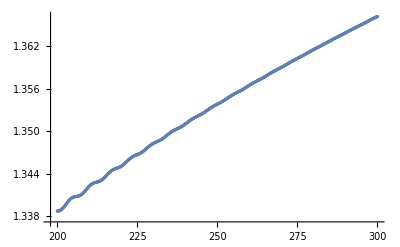

```mathematica
lt=200;
length=100;
plotpoints=Table[{t,f[t,0.05]},{t,lt,lt+length,0.1}];
ListPlot[plotpoints]
```

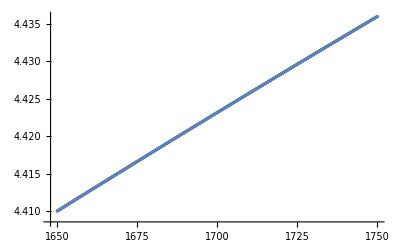

```mathematica
lt=1650;
length=100;
plotpoints=Table[{t,f[t,0.1]},{t,lt,lt+length,0.1}];
ListPlot[plotpoints]
```

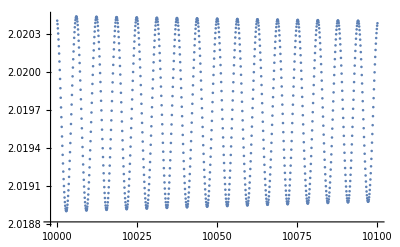

```mathematica
lt=10000;
length=100;
plotpoints=Table[{t,f[t,0.001]},{t,lt,lt+length,0.1}];
ListPlot[plotpoints]
```

```mathematica
Export["pointsmsd.csv",plotpoints,"Table"]
```

pointsmsd.csv

```mathematica
plotpoints
```

{{10000.,2.02041},{10000.1,2.02038},{10000.2,2.02035},{10000.3,2.02031},{10000.4,2.02026},{10000.5,2.02021},{10000.6,2.02015},{10000.7,2.02008},{10000.8,2.02002},{10000.9,2.01995},{10001.,2.01987},{10001.1,2.0198},{10001.2,2.01972},{10001.3,2.01964},{10001.4,2.01957},{10001.5,2.01949},{10001.6,2.01942},{10001.7,2.01934},{10001.8,2.01928},{10001.9,2.01921},{10002.,2.01915},{10002.1,2.0191},{10002.2,2.01905},{10002.3,2.01901},{10002.4,2.01897},{10002.5,2.01894},{10002.6,2.01892},{10002.7,2.01891},{10002.8,2.0189},{10002.9,2.0189},{10003.,2.01891},{10003.1,2.01893},{10003.2,2.01895},{10003.3,2.01898},{10003.4,2.01902},{10003.5,2.01906},{10003.6,2.01911},{10003.7,2.01917},{10003.8,2.01923},{10003.9,2.0193},{10004.,2.01937},{10004.1,2.01944},{10004.2,2.01951},{10004.3,2.01959},{10004.4,2.01967},{10004.5,2.01974},{10004.6,2.01982},{10004.7,2.01989},{10004.8,2.01997},{10004.9,2.02004},{10005.,2.0201},{10005.1,2.02016},{10005.2,2.02022},{10005.3,2.02027},{10005.4,2.02032},{10005.5,2.02035},{10005.6,2.02039},{10005.7,2.02041},{10005.8,2.02043},{10005.9,2.02044},{10006.,2.02044},{10006.1,2.02044},{10006.2,2.02042},{10006.3,2.0204},{10006.4,2.02037},{10006.5,2.02034},{10006.6,2.0203},{10006.7,2.02025},{10006.8,2.02019},{10006.9,2.02014},{10007.,2.02007},{10007.1,2.02},{10007.2,2.01993},{10007.3,2.01986},{10007.4,2.01978},{10007.5,2.01971},{10007.6,2.01963},{10007.7,2.01955},{10007.8,2.01948},{10007.9,2.01941},{10008.,2.01934},{10008.1,2.01927},{10008.2,2.0192},{10008.3,2.01915},{10008.4,2.01909},{10008.5,2.01905},{10008.6,2.019},{10008.7,2.01897},{10008.8,2.01894},{10008.9,2.01892},{10009.,2.01891},{10009.1,2.0189},{10009.2,2.01891},{10009.3,2.01892},{10009.4,2.01893},{10009.5,2.01896},{10009.6,2.01899},{10009.7,2.01903},{10009.8,2.01908},{10009.9,2.01913},{10010.,2.01918},{10010.1,2.01924},{10010.2,2.01931},{10010.3,2.01938},{10010.4,2.01945},{10010.5,2.01953},{10010.6,2.0196},{10010.7,2.01968},{10010.8,2.01976},{10010.9,2.01983},{10011.,2.01991},{10011.1,2.01998},{10011.2,2.02005},{10011.3,2.02011},{10011.4,2.02017},{10011.5,2.02023},{10011.6,2.02028},{10011.7,2.02032},{10011.8,2.02036},{10011.9,2.02039},{10012.,2.02041},{10012.1,2.02043},{10012.2,2.02044},{10012.3,2.02044},{10012.4,2.02043},{10012.5,2.02042},{10012.6,2.02039},{10012.7,2.02037},{10012.8,2.02033},{10012.9,2.02029},{10013.,2.02024},{10013.1,2.02018},{10013.2,2.02012},{10013.3,2.02006},{10013.4,2.01999},{10013.5,2.01992},{10013.6,2.01985},{10013.7,2.01977},{10013.8,2.0197},{10013.9,2.01962},{10014.,2.01954},{10014.1,2.01947},{10014.2,2.0194},{10014.3,2.01933},{10014.4,2.01926},{10014.5,2.0192},{10014.6,2.01914},{10014.7,2.01909},{10014.8,2.01904},{10014.9,2.019},{10015.,2.01897},{10015.1,2.01894},{10015.2,2.01892},{10015.3,2.01891},{10015.4,2.01891},{10015.5,2.01891},{10015.6,2.01892},{10015.7,2.01894},{10015.8,2.01897},{10015.9,2.019},{10016.,2.01904},{10016.1,2.01909},{10016.2,2.01914},{10016.3,2.0192},{10016.4,2.01926},{10016.5,2.01933},{10016.6,2.01939},{10016.7,2.01947},{10016.8,2.01954},{10016.9,2.01962},{10017.,2.01969},{10017.1,2.01977},{10017.2,2.01984},{10017.3,2.01992},{10017.4,2.01999},{10017.5,2.02006},{10017.6,2.02012},{10017.7,2.02018},{10017.8,2.02023},{10017.9,2.02028},{10018.,2.02033},{10018.1,2.02036},{10018.2,2.02039},{10018.3,2.02041},{10018.4,2.02043},{10018.5,2.02044},{10018.6,2.02043},{10018.7,2.02043},{10018.8,2.02041},{10018.9,2.02039},{10019.,2.02036},{10019.1,2.02032},{10019.2,2.02028},{10019.3,2.02023},{10019.4,2.02017},{10019.5,2.02011},{10019.6,2.02005},{10019.7,2.01998},{10019.8,2.01991},{10019.9,2.01984},{10020.,2.01976},{10020.1,2.01968},{10020.2,2.01961},{10020.3,2.01953},{10020.4,2.01946},{10020.5,2.01939},{10020.6,2.01932},{10020.7,2.01925},{10020.8,2.01919},{10020.9,2.01914},{10021.,2.01908},{10021.1,2.01904},{10021.2,2.019},{10021.3,2.01897},{10021.4,2.01894},{10021.5,2.01893},{10021.6,2.01892},{10021.7,2.01891},{10021.8,2.01892},{10021.9,2.01893},{10022.,2.01895},{10022.1,2.01898},{10022.2,2.01901},{10022.3,2.01905},{10022.4,2.0191},{10022.5,2.01915},{10022.6,2.01921},{10022.7,2.01927},{10022.8,2.01934},{10022.9,2.01941},{10023.,2.01948},{10023.1,2.01956},{10023.2,2.01963},{10023.3,2.01971},{10023.4,2.01978},{10023.5,2.01986},{10023.6,2.01993},{10023.7,2.02},{10023.8,2.02007},{10023.9,2.02013},{10024.,2.02019},{10024.1,2.02024},{10024.2,2.02029},{10024.3,2.02033},{10024.4,2.02037},{10024.5,2.02039},{10024.6,2.02041},{10024.7,2.02043},{10024.8,2.02043},{10024.9,2.02043},{10025.,2.02042},{10025.1,2.02041},{10025.2,2.02038},{10025.3,2.02035},{10025.4,2.02031},{10025.5,2.02027},{10025.6,2.02022},{10025.7,2.02016},{10025.8,2.0201},{10025.9,2.02004},{10026.,2.01997},{10026.1,2.0199},{10026.2,2.01982},{10026.3,2.01975},{10026.4,2.01967},{10026.5,2.0196},{10026.6,2.01952},{10026.7,2.01945},{10026.8,2.01938},{10026.9,2.01931},{10027.,2.01925},{10027.1,2.01919},{10027.2,2.01913},{10027.3,2.01908},{10027.4,2.01904},{10027.5,2.019},{10027.6,2.01897},{10027.7,2.01895},{10027.8,2.01893},{10027.9,2.01892},{10028.,2.01892},{10028.1,2.01892},{10028.2,2.01894},{10028.3,2.01896},{10028.4,2.01899},{10028.5,2.01902},{10028.6,2.01906},{10028.7,2.01911},{10028.8,2.01917},{10028.9,2.01922},{10029.,2.01929},{10029.1,2.01935},{10029.2,2.01942},{10029.3,2.0195},{10029.4,2.01957},{10029.5,2.01965},{10029.6,2.01972},{10029.7,2.0198},{10029.8,2.01987},{10029.9,2.01994},{10030.,2.02001},{10030.1,2.02008},{10030.2,2.02014},{10030.3,2.0202},{10030.4,2.02025},{10030.5,2.02029},{10030.6,2.02033},{10030.7,2.02037},{10030.8,2.0204},{10030.9,2.02041},{10031.,2.02043},{10031.1,2.02043},{10031.2,2.02043},{10031.3,2.02042},{10031.4,2.0204},{10031.5,2.02037},{10031.6,2.02034},{10031.7,2.0203},{10031.8,2.02026},{10031.9,2.02021},{10032.,2.02015},{10032.1,2.02009},{10032.2,2.02002},{10032.3,2.01996},{10032.4,2.01989},{10032.5,2.01981},{10032.6,2.01974},{10032.7,2.01966},{10032.8,2.01959},{10032.9,2.01951},{10033.,2.01944},{10033.1,2.01937},{10033.2,2.0193},{10033.3,2.01924},{10033.4,2.01918},{10033.5,2.01913},{10033.6,2.01908},{10033.7,2.01903},{10033.8,2.019},{10033.9,2.01897},{10034.,2.01895},{10034.1,2.01893},{10034.2,2.01892},{10034.3,2.01892},{10034.4,2.01893},{10034.5,2.01895},{10034.6,2.01897},{10034.7,2.019},{10034.8,2.01903},{10034.9,2.01908},{10035.,2.01913},{10035.1,2.01918},{10035.2,2.01924},{10035.3,2.0193},{10035.4,2.01937},{10035.5,2.01944},{10035.6,2.01951},{10035.7,2.01958},{10035.8,2.01966},{10035.9,2.01974},{10036.,2.01981},{10036.1,2.01988},{10036.2,2.01995},{10036.3,2.02002},{10036.4,2.02009},{10036.5,2.02015},{10036.6,2.0202},{10036.7,2.02026},{10036.8,2.0203},{10036.9,2.02034},{10037.,2.02037},{10037.1,2.0204},{10037.2,2.02041},{10037.3,2.02043},{10037.4,2.02043},{10037.5,2.02042},{10037.6,2.02041},{10037.7,2.02039},{10037.8,2.02037},{10037.9,2.02033},{10038.,2.02029},{10038.1,2.02025},{10038.2,2.0202},{10038.3,2.02014},{10038.4,2.02008},{10038.5,2.02001},{10038.6,2.01994},{10038.7,2.01987},{10038.8,2.0198},{10038.9,2.01973},{10039.,2.01965},{10039.1,2.01958},{10039.2,2.0195},{10039.3,2.01943},{10039.4,2.01936},{10039.5,2.01929},{10039.6,2.01923},{10039.7,2.01917},{10039.8,2.01912},{10039.9,2.01907},{10040.,2.01903},{10040.1,2.019},{10040.2,2.01897},{10040.3,2.01895},{10040.4,2.01893},{10040.5,2.01893},{10040.6,2.01893},{10040.7,2.01894},{10040.8,2.01895},{10040.9,2.01898},{10041.,2.01901},{10041.1,2.01905},{10041.2,2.01909},{10041.3,2.01914},{10041.4,2.01919},{10041.5,2.01925},{10041.6,2.01932},{10041.7,2.01938},{10041.8,2.01945},{10041.9,2.01953},{10042.,2.0196},{10042.1,2.01967},{10042.2,2.01975},{10042.3,2.01982},{10042.4,2.0199},{10042.5,2.01997},{10042.6,2.02003},{10042.7,2.0201},{10042.8,2.02016},{10042.9,2.02021},{10043.,2.02026},{10043.1,2.02031},{10043.2,2.02034},{10043.3,2.02037},{10043.4,2.0204},{10043.5,2.02041},{10043.6,2.02042},{10043.7,2.02043},{10043.8,2.02042},{10043.9,2.02041},{10044.,2.02039},{10044.1,2.02036},{10044.2,2.02033},{10044.3,2.02029},{10044.4,2.02024},{10044.5,2.02019},{10044.6,2.02013},{10044.7,2.02007},{10044.8,2.02},{10044.9,2.01993},{10045.,2.01986},{10045.1,2.01979},{10045.2,2.01971},{10045.3,2.01964},{10045.4,2.01957},{10045.5,2.01949},{10045.6,2.01942},{10045.7,2.01935},{10045.8,2.01929},{10045.9,2.01923},{10046.,2.01917},{10046.1,2.01912},{10046.2,2.01907},{10046.3,2.01903},{10046.4,2.019},{10046.5,2.01897},{10046.6,2.01895},{10046.7,2.01894},{10046.8,2.01893},{10046.9,2.01894},{10047.,2.01895},{10047.1,2.01896},{10047.2,2.01899},{10047.3,2.01902},{10047.4,2.01906},{10047.5,2.0191},{10047.6,2.01915},{10047.7,2.01921},{10047.8,2.01927},{10047.9,2.01933},{10048.,2.0194},{10048.1,2.01947},{10048.2,2.01954},{10048.3,2.01961},{10048.4,2.01969},{10048.5,2.01976},{10048.6,2.01984},{10048.7,2.01991},{10048.8,2.01998},{10048.9,2.02004},{10049.,2.02011},{10049.1,2.02017},{10049.2,2.02022},{10049.3,2.02027},{10049.4,2.02031},{10049.5,2.02035},{10049.6,2.02038},{10049.7,2.0204},{10049.8,2.02041},{10049.9,2.02042},{10050.,2.02042},{10050.1,2.02042},{10050.2,2.0204},{10050.3,2.02038},{10050.4,2.02035},{10050.5,2.02032},{10050.6,2.02028},{10050.7,2.02023},{10050.8,2.02018},{10050.9,2.02012},{10051.,2.02006},{10051.1,2.01999},{10051.2,2.01992},{10051.3,2.01985},{10051.4,2.01978},{10051.5,2.0197},{10051.6,2.01963},{10051.7,2.01955},{10051.8,2.01948},{10051.9,2.01941},{10052.,2.01934},{10052.1,2.01928},{10052.2,2.01922},{10052.3,2.01916},{10052.4,2.01911},{10052.5,2.01907},{10052.6,2.01903},{10052.7,2.019},{10052.8,2.01897},{10052.9,2.01895},{10053.,2.01894},{10053.1,2.01894},{10053.2,2.01894},{10053.3,2.01895},{10053.4,2.01897},{10053.5,2.019},{10053.6,2.01903},{10053.7,2.01907},{10053.8,2.01911},{10053.9,2.01916},{10054.,2.01922},{10054.1,2.01928},{10054.2,2.01934},{10054.3,2.01941},{10054.4,2.01948},{10054.5,2.01955},{10054.6,2.01963},{10054.7,2.0197},{10054.8,2.01978},{10054.9,2.01985},{10055.,2.01992},{10055.1,2.01999},{10055.2,2.02005},{10055.3,2.02012},{10055.4,2.02017},{10055.5,2.02023},{10055.6,2.02027},{10055.7,2.02031},{10055.8,2.02035},{10055.9,2.02038},{10056.,2.0204},{10056.1,2.02041},{10056.2,2.02042},{10056.3,2.02042},{10056.4,2.02041},{10056.5,2.0204},{10056.6,2.02037},{10056.7,2.02034},{10056.8,2.02031},{10056.9,2.02027},{10057.,2.02022},{10057.1,2.02017},{10057.2,2.02011},{10057.3,2.02004},{10057.4,2.01998},{10057.5,2.01991},{10057.6,2.01984},{10057.7,2.01976},{10057.8,2.01969},{10057.9,2.01962},{10058.,2.01954},{10058.1,2.01947},{10058.2,2.0194},{10058.3,2.01934},{10058.4,2.01927},{10058.5,2.01921},{10058.6,2.01916},{10058.7,2.01911},{10058.8,2.01907},{10058.9,2.01903},{10059.,2.019},{10059.1,2.01897},{10059.2,2.01896},{10059.3,2.01895},{10059.4,2.01894},{10059.5,2.01895},{10059.6,2.01896},{10059.7,2.01898},{10059.8,2.01901},{10059.9,2.01904},{10060.,2.01908},{10060.1,2.01912},{10060.2,2.01918},{10060.3,2.01923},{10060.4,2.01929},{10060.5,2.01936},{10060.6,2.01943},{10060.7,2.0195},{10060.8,2.01957},{10060.9,2.01964},{10061.,2.01971},{10061.1,2.01979},{10061.2,2.01986},{10061.3,2.01993},{10061.4,2.02},{10061.5,2.02006},{10061.6,2.02013},{10061.7,2.02018},{10061.8,2.02023},{10061.9,2.02028},{10062.,2.02032},{10062.1,2.02035},{10062.2,2.02038},{10062.3,2.0204},{10062.4,2.02041},{10062.5,2.02042},{10062.6,2.02042},{10062.7,2.02041},{10062.8,2.02039},{10062.9,2.02037},{10063.,2.02034},{10063.1,2.0203},{10063.2,2.02026},{10063.3,2.02021},{10063.4,2.02015},{10063.5,2.0201},{10063.6,2.02003},{10063.7,2.01997},{10063.8,2.0199},{10063.9,2.01983},{10064.,2.01975},{10064.1,2.01968},{10064.2,2.01961},{10064.3,2.01953},{10064.4,2.01946},{10064.5,2.01939},{10064.6,2.01933},{10064.7,2.01927},{10064.8,2.01921},{10064.9,2.01915},{10065.,2.01911},{10065.1,2.01906},{10065.2,2.01903},{10065.3,2.019},{10065.4,2.01897},{10065.5,2.01896},{10065.6,2.01895},{10065.7,2.01895},{10065.8,2.01895},{10065.9,2.01897},{10066.,2.01899},{10066.1,2.01902},{10066.2,2.01905},{10066.3,2.01909},{10066.4,2.01914},{10066.5,2.01919},{10066.6,2.01925},{10066.7,2.01931},{10066.8,2.01937},{10066.9,2.01944},{10067.,2.01951},{10067.1,2.01958},{10067.2,2.01965},{10067.3,2.01973},{10067.4,2.0198},{10067.5,2.01987},{10067.6,2.01994},{10067.7,2.02001},{10067.8,2.02007},{10067.9,2.02013},{10068.,2.02019},{10068.1,2.02024},{10068.2,2.02028},{10068.3,2.02032},{10068.4,2.02036},{10068.5,2.02038},{10068.6,2.0204},{10068.7,2.02041},{10068.8,2.02042},{10068.9,2.02041},{10069.,2.0204},{10069.1,2.02039},{10069.2,2.02036},{10069.3,2.02033},{10069.4,2.02029},{10069.5,2.02025},{10069.6,2.0202},{10069.7,2.02014},{10069.8,2.02008},{10069.9,2.02002},{10070.,2.01996},{10070.1,2.01989},{10070.2,2.01981},{10070.3,2.01974},{10070.4,2.01967},{10070.5,2.0196},{10070.6,2.01952},{10070.7,2.01945},{10070.8,2.01939},{10070.9,2.01932},{10071.,2.01926},{10071.1,2.0192},{10071.2,2.01915},{10071.3,2.0191},{10071.4,2.01906},{10071.5,2.01903},{10071.6,2.019},{10071.7,2.01898},{10071.8,2.01896},{10071.9,2.01895},{10072.,2.01895},{10072.1,2.01896},{10072.2,2.01898},{10072.3,2.019},{10072.4,2.01903},{10072.5,2.01906},{10072.6,2.0191},{10072.7,2.01915},{10072.8,2.0192},{10072.9,2.01926},{10073.,2.01932},{10073.1,2.01939},{10073.2,2.01945},{10073.3,2.01952},{10073.4,2.0196},{10073.5,2.01967},{10073.6,2.01974},{10073.7,2.01981},{10073.8,2.01989},{10073.9,2.01995},{10074.,2.02002},{10074.1,2.02008},{10074.2,2.02014},{10074.3,2.0202},{10074.4,2.02025},{10074.5,2.02029},{10074.6,2.02033},{10074.7,2.02036},{10074.8,2.02038},{10074.9,2.0204},{10075.,2.02041},{10075.1,2.02041},{10075.2,2.02041},{10075.3,2.0204},{10075.4,2.02038},{10075.5,2.02035},{10075.6,2.02032},{10075.7,2.02028},{10075.8,2.02024},{10075.9,2.02019},{10076.,2.02013},{10076.1,2.02007},{10076.2,2.02001},{10076.3,2.01994},{10076.4,2.01987},{10076.5,2.0198},{10076.6,2.01973},{10076.7,2.01966},{10076.8,2.01959},{10076.9,2.01951},{10077.,2.01944},{10077.1,2.01938},{10077.2,2.01931},{10077.3,2.01925},{10077.4,2.0192},{10077.5,2.01914},{10077.6,2.0191},{10077.7,2.01906},{10077.8,2.01902},{10077.9,2.019},{10078.,2.01898},{10078.1,2.01896},{10078.2,2.01896},{10078.3,2.01896},{10078.4,2.01897},{10078.5,2.01898},{10078.6,2.01901},{10078.7,2.01904},{10078.8,2.01907},{10078.9,2.01911},{10079.,2.01916},{10079.1,2.01921},{10079.2,2.01927},{10079.3,2.01933},{10079.4,2.0194},{10079.5,2.01947},{10079.6,2.01954},{10079.7,2.01961},{10079.8,2.01968},{10079.9,2.01975},{10080.,2.01983},{10080.1,2.0199},{10080.2,2.01997},{10080.3,2.02003},{10080.4,2.02009},{10080.5,2.02015},{10080.6,2.0202},{10080.7,2.02025},{10080.8,2.02029},{10080.9,2.02033},{10081.,2.02036},{10081.1,2.02038},{10081.2,2.0204},{10081.3,2.02041},{10081.4,2.02041},{10081.5,2.02041},{10081.6,2.02039},{10081.7,2.02037},{10081.8,2.02035},{10081.9,2.02031},{10082.,2.02027},{10082.1,2.02023},{10082.2,2.02018},{10082.3,2.02012},{10082.4,2.02006},{10082.5,2.02},{10082.6,2.01993},{10082.7,2.01986},{10082.8,2.01979},{10082.9,2.01972},{10083.,2.01965},{10083.1,2.01958},{10083.2,2.0195},{10083.3,2.01944},{10083.4,2.01937},{10083.5,2.01931},{10083.6,2.01925},{10083.7,2.01919},{10083.8,2.01914},{10083.9,2.0191},{10084.,2.01906},{10084.1,2.01902},{10084.2,2.019},{10084.3,2.01898},{10084.4,2.01897},{10084.5,2.01896},{10084.6,2.01897},{10084.7,2.01897},{10084.8,2.01899},{10084.9,2.01902},{10085.,2.01905},{10085.1,2.01908},{10085.2,2.01913},{10085.3,2.01917},{10085.4,2.01923},{10085.5,2.01929},{10085.6,2.01935},{10085.7,2.01941},{10085.8,2.01948},{10085.9,2.01955},{10086.,2.01962},{10086.1,2.0197},{10086.2,2.01977},{10086.3,2.01984},{10086.4,2.01991},{10086.5,2.01998},{10086.6,2.02004},{10086.7,2.0201},{10086.8,2.02016},{10086.9,2.02021},{10087.,2.02026},{10087.1,2.0203},{10087.2,2.02033},{10087.3,2.02036},{10087.4,2.02039},{10087.5,2.0204},{10087.6,2.02041},{10087.7,2.02041},{10087.8,2.0204},{10087.9,2.02039},{10088.,2.02037},{10088.1,2.02034},{10088.2,2.02031},{10088.3,2.02027},{10088.4,2.02022},{10088.5,2.02017},{10088.6,2.02011},{10088.7,2.02005},{10088.8,2.01999},{10088.9,2.01992},{10089.,2.01985},{10089.1,2.01978},{10089.2,2.01971},{10089.3,2.01964},{10089.4,2.01957},{10089.5,2.01949},{10089.6,2.01943},{10089.7,2.01936},{10089.8,2.0193},{10089.9,2.01924},{10090.,2.01919},{10090.1,2.01914},{10090.2,2.01909},{10090.3,2.01906},{10090.4,2.01902},{10090.5,2.019},{10090.6,2.01898},{10090.7,2.01897},{10090.8,2.01897},{10090.9,2.01897},{10091.,2.01898},{10091.1,2.019},{10091.2,2.01902},{10091.3,2.01906},{10091.4,2.01909},{10091.5,2.01914},{10091.6,2.01919},{10091.7,2.01924},{10091.8,2.0193},{10091.9,2.01936},{10092.,2.01943},{10092.1,2.0195},{10092.2,2.01957},{10092.3,2.01964},{10092.4,2.01971},{10092.5,2.01978},{10092.6,2.01985},{10092.7,2.01992},{10092.8,2.01999},{10092.9,2.02005},{10093.,2.02011},{10093.1,2.02017},{10093.2,2.02022},{10093.3,2.02026},{10093.4,2.0203},{10093.5,2.02034},{10093.6,2.02037},{10093.7,2.02039},{10093.8,2.0204},{10093.9,2.02041},{10094.,2.02041},{10094.1,2.0204},{10094.2,2.02038},{10094.3,2.02036},{10094.4,2.02033},{10094.5,2.0203},{10094.6,2.02026},{10094.7,2.02021},{10094.8,2.02016},{10094.9,2.0201},{10095.,2.02004},{10095.1,2.01998},{10095.2,2.01991},{10095.3,2.01984},{10095.4,2.01977},{10095.5,2.0197},{10095.6,2.01963},{10095.7,2.01956},{10095.8,2.01949},{10095.9,2.01942},{10096.,2.01935},{10096.1,2.01929},{10096.2,2.01923},{10096.3,2.01918},{10096.4,2.01913},{10096.5,2.01909},{10096.6,2.01905},{10096.7,2.01902},{10096.8,2.019},{10096.9,2.01898},{10097.,2.01897},{10097.1,2.01897},{10097.2,2.01898},{10097.3,2.01899},{10097.4,2.01901},{10097.5,2.01903},{10097.6,2.01907},{10097.7,2.0191},{10097.8,2.01915},{10097.9,2.0192},{10098.,2.01925},{10098.1,2.01931},{10098.2,2.01937},{10098.3,2.01944},{10098.4,2.01951},{10098.5,2.01958},{10098.6,2.01965},{10098.7,2.01972},{10098.8,2.01979},{10098.9,2.01986},{10099.,2.01993},{10099.1,2.02},{10099.2,2.02006},{10099.3,2.02012},{10099.4,2.02018},{10099.5,2.02023},{10099.6,2.02027},{10099.7,2.02031},{10099.8,2.02034},{10099.9,2.02037},{10100.,2.02039}}

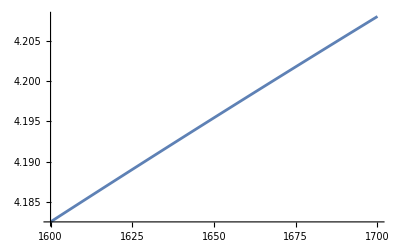

```mathematica
Plot[2 t^0.1,{t,1600,1700}]
```

```mathematica
f1[t_,a_]:=t^2 MittagLefflerE[2-a,3,-t^(2-a)];
msd[t_,a_]:=2NIntegrate[(x MittagLefflerE[2-a,2,-x^(2-a)])^2,{x,0,t},AccuracyGoal->3]+(t MittagLefflerE[2-a,2,-t^(2-a)])^2
```

```mathematica
MittagLefflerE
```

```mathematica
points=ParallelTable[{t,msd[t,a]},{a,0.01,0.1,0.02},{t,0,25,0.1}];
```

```mathematica
Export["datapoints.csv",points,"List"]
```

datapoints.csv

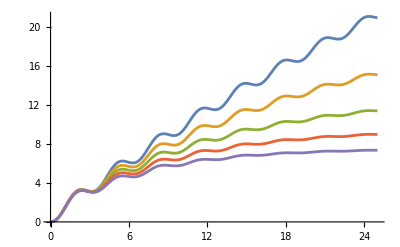

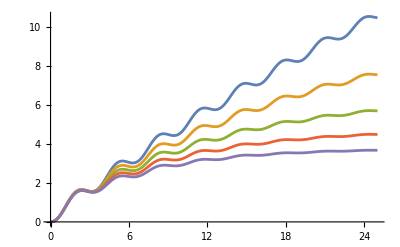

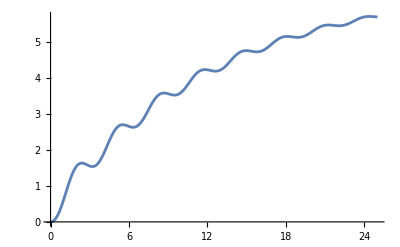

```mathematica
ListLinePlot[points]
```

```mathematica
7Pi//N
```

21.9911